PageRank Linear Algebra Formulation

## The Example Graph

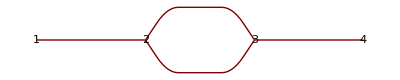

```mathematica
n = 4;
GraphPlot[{1 -> 2, 2 -> 3, 3 -> 4, 3 -> 2}, VertexLabeling -> True]
```

## The Stochastic Adjacency/Transition Matrix: M

```mathematica
M = {{0,0,0,0},{1,0,1/2,1},{0,1,0,0},{0,0,1/2,0}};
```

(0 | 0 | 0 | 0
1 | 0 | 1/2 | 1
0 | 1 | 0 | 0
0 | 0 | 1/2 | 0)

## The Dampening Factor

```mathematica
d = 0.85;
```

## The initial Distribution

```mathematica
PR0 = {1/n,1/n,1/n,1/n};
```

(1/4
1/4
1/4
1/4)

## The Teleportation Vector

```mathematica
P = {(1-d)/n,(1-d)/n,(1-d)/n,(1-d)/n};
```

(0.0375
0.0375
0.0375
0.0375)

## The Iterative Formula

PR_(i+1) = dM  · PR_i + P

## The Iterative Formula

```mathematica
iterations = 50;
PRI = PR0;
For[i=0,i<iterations,i++,PRI =((d*M).PRI) + P];
PR = PRI;
```

PageRank for our graph:

(0.0375
0.394149
0.372527
0.195824)

Kim Hammar

kimham@kth.se

12/10-2017